```mathematica
<<myFunctionsMathematica8.m
```

SetDelayed::write: Tag Real in 20.[z_] is Protected.

SetDelayed::write: Tag List in {1/2 + « 1031 »\ ⅈ, -« 644 » - « 639 »\ ⅈ, -« 644 » + « 647 »\ ⅈ, -« 644 », -« 644 »}[breakbound_, ds_, n_] is Protected.

SetDelayed::write: Tag Real in 20.[z_] is Protected.

General::stop: Further output of SetDelayed :: write will be suppressed during this calculation.

{Temporary}

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

```mathematica
streamzeros=OpenRead["betterbarryzeros"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
```

```mathematica
First[betterbarryzeroslist]
```

0.5+14.13472514173469379045725198356247027078425711569924317568556746014996342980925676494901039317156101277920297154879743676614269146988225458250536323944713778041338123720597054962195586586020055556672583601077370020541098266150754278051744259130625448197865107230493872562973832157742039521572567480933214003499046803434626731442092037738548714137831735639699536542811307968053149168852906782082298049264338666734623320078758761792005604868054356801444424651065597568665903228686510544859444320624072727032094274522213048748720924123851418351460542790152447833835425453344004487936806761697300819000731393854983736215013045167269683892003917628512321285422052396913342583227533516406016976352756375896953767492033612720925999173042707568308795118445348918008630082648312516911271068291052375961797743181517071354531677549515382893784903647470972701994848553220925357435790922612524773659551801697523346121397731600535412592674745572587780147260983080897860071253208750939599796666067537838121489190886 ⅈ

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  1

fixed point ~ -20.1312

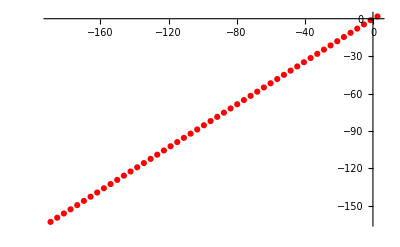
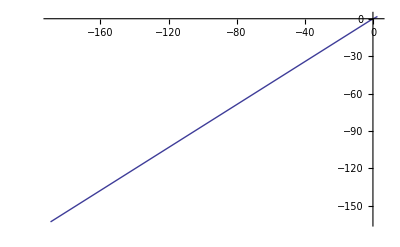

elasped seconds   158.43992

```mathematica
start=SessionTime[];
streamzeros=OpenRead["betterbarryzeros"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxpts24may16no11"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenWrite["realfxNrhoNrun31may16no5"];
precision=500;
For[n=0,n<1,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*Im[betterbarryzeroslist[[n]]];
fx=N[fxlist[[n,2]],1000];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<50,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]];
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```

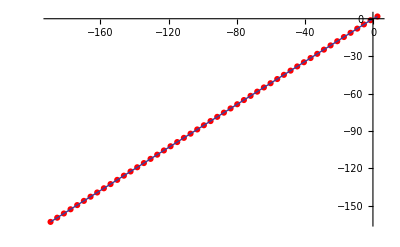

```mathematica
Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]]
```

```mathematica
start=SessionTime[];
streamzeros=OpenRead["betterbarryzeros"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxpts24may16no11"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenWrite["realfxNrhoNrun31may16no6"];
precision=500;
For[n=0,n<1,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*Im[betterbarryzeroslist[[n]]];
fx=N[fxlist[[n,2]],1000];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<100,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]];
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

## leaf5.7r1c2

n  1

fixed point ~ -20.1312

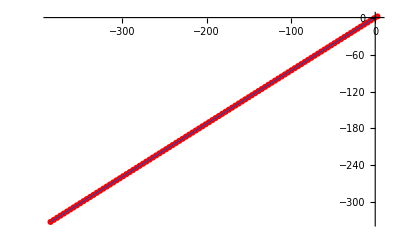

elasped seconds   253.52207

```mathematica
start=SessionTime[];
streamzeros=OpenRead["betterbarryzeros"];
betterbarryzeroslist=ReadList[streamzeros];
Close[streamzeros];
streamfx=OpenRead["realfxpts24may16no11"];
fxlist=ReadList[streamfx];
Close[streamfx];

stream1=OpenAppend["realfxNrhoNrun31may16no5"];
precision=500;
For[n=1,n<50,n++;
orbit={};
shortorbit={};
data={};
orbitpairs={};
args={};
thetaset={};
errorpairs={};
relerrorpairs={};
targetzero=1/2+I*Im[betterbarryzeroslist[[n]]];
fx=N[fxlist[[n,2]],1000];
Print["&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&"];
Print["n  ",n];
Print["fixed point ~ ",N[Round[fx,1/10^10]]];

k=1;
zr=targetzero;
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
arg=Arg[zr-fx];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair];


For[k=1,k<50,k++;
startcenter=fx;
x=orbit[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision+50,WorkingPrecision->precision+100][[1,2]];
Write[stream1,{n,k,zr}];
orbit=Append[orbit,zr];
shortorbit=Append[shortorbit,zr];
arg=Arg[zr-fx];
While[Not[arg-Last[args]>1],arg=arg+2*Pi];
args=Append[args,arg];
la=Re[Log[Abs[zr-fx]]];
orbitpair={la*Cos[arg],la*Sin[arg]};
orbitpairs=Append[orbitpairs,orbitpair]
](*close k loop *)

Print[Show[ListPlot[orbitpairs,PlotStyle->{Red,PointSize[.011]}],ListPlot[orbitpairs,Joined->True]]];
];(* close n-loop *)
Close[stream1];
Print["elasped seconds   ",SessionTime[]-start]
```

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

## leaf5.7r2c2

n  2

fixed point ~ -21.9855

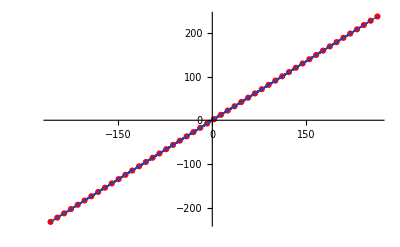

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

## leaf5.7r3c2

n  3

fixed point ~ -24.0011

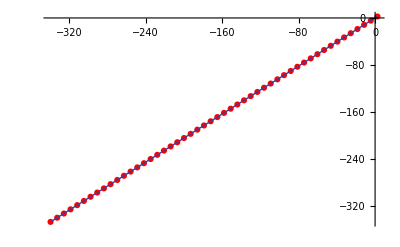

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

## leaf5.7r4c2

n  4

fixed point ~ -25.9999

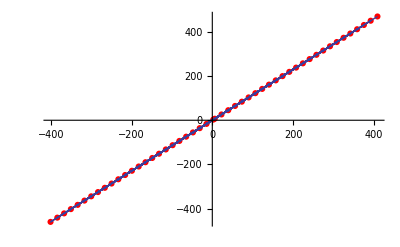

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  5

fixed point ~ -28.

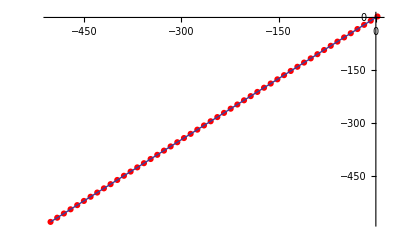

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  6

fixed point ~ -30.

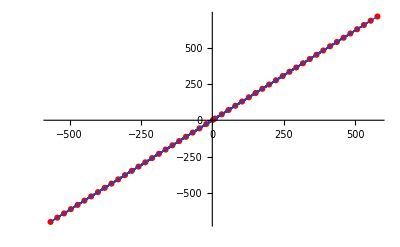

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  7

fixed point ~ -32.

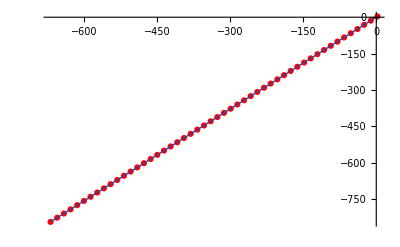

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  8

fixed point ~ -34.

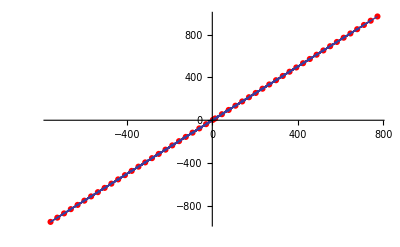

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  9

fixed point ~ -36.

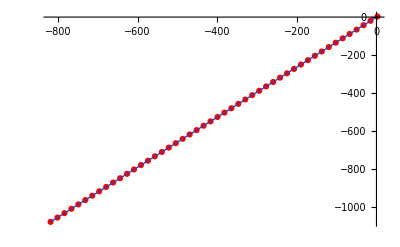

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  10

fixed point ~ -38.

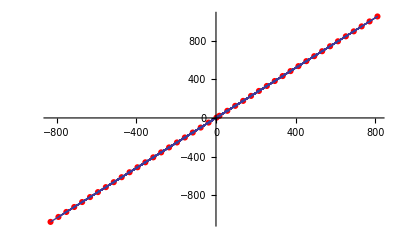

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  11

fixed point ~ -40.

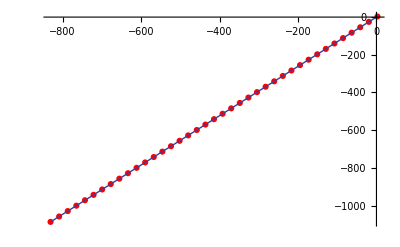

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  12

fixed point ~ -42.

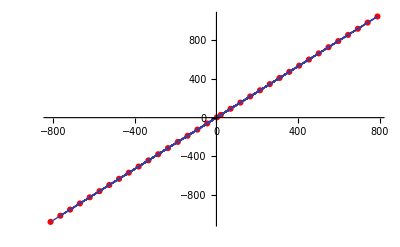

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  13

fixed point ~ -44.

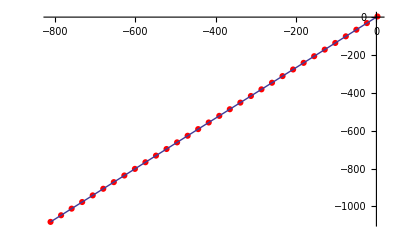

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  14

fixed point ~ -46.

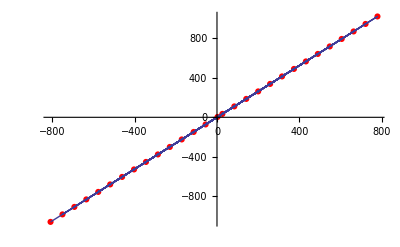

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  15

fixed point ~ -48.

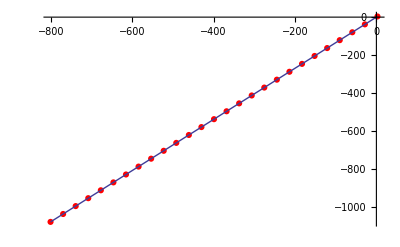

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  16

fixed point ~ -50.

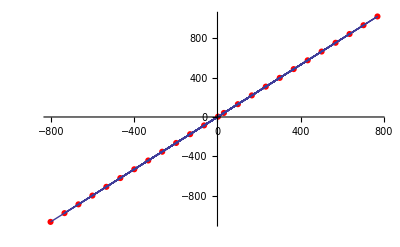

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  17

fixed point ~ -52.

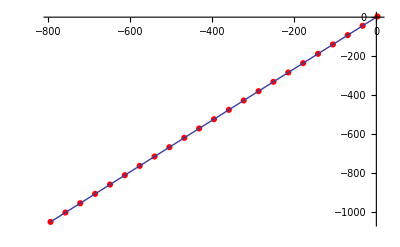

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  18

fixed point ~ -54.

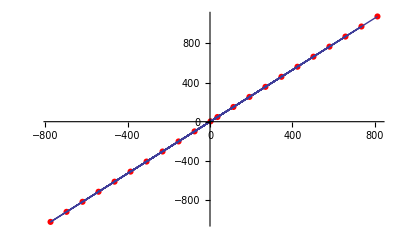

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  19

fixed point ~ -56.

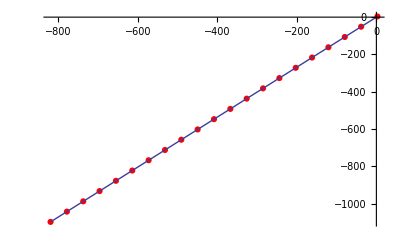

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  20

fixed point ~ -58.

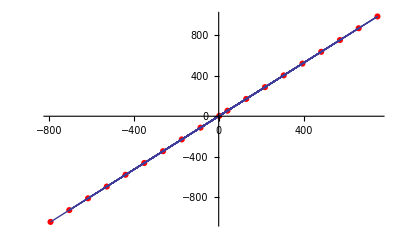

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  21

fixed point ~ -60.

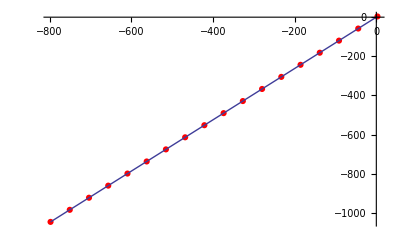

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  22

fixed point ~ -62.

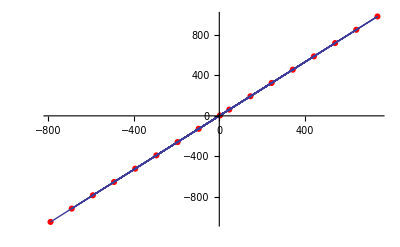

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  23

fixed point ~ -64.

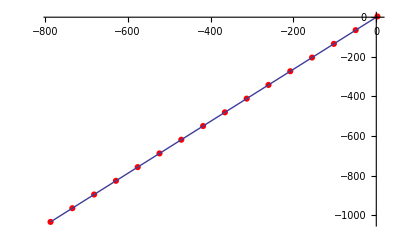

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  24

fixed point ~ -66.

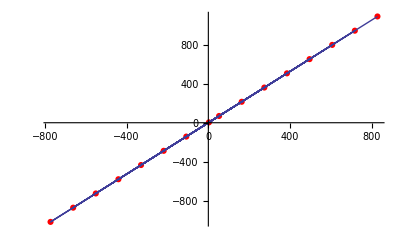

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  25

fixed point ~ -68.

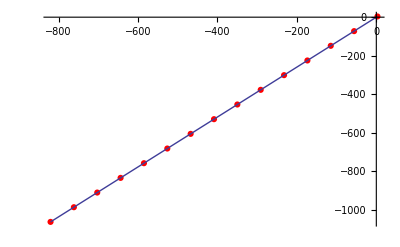

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  26

fixed point ~ -70.

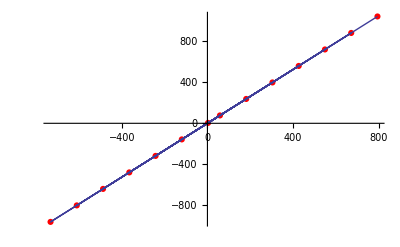

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  27

fixed point ~ -72.

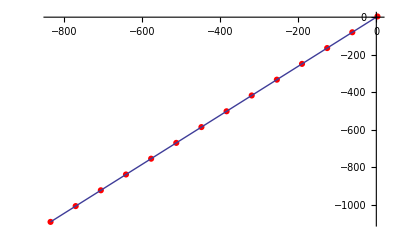

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  28

fixed point ~ -74.

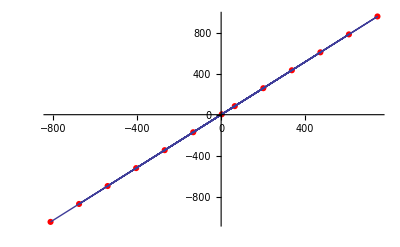

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  29

fixed point ~ -76.

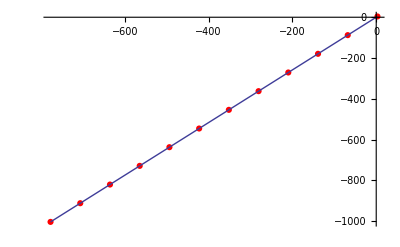

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  30

fixed point ~ -78.

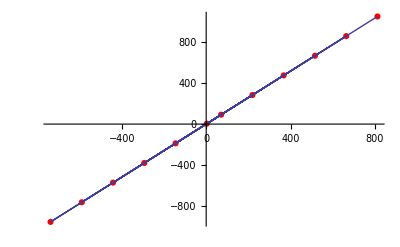

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  31

fixed point ~ -80.

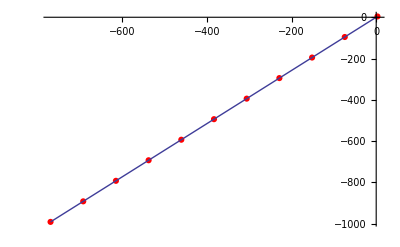

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  32

fixed point ~ -82.

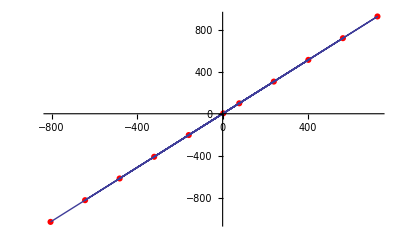

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  33

fixed point ~ -84.

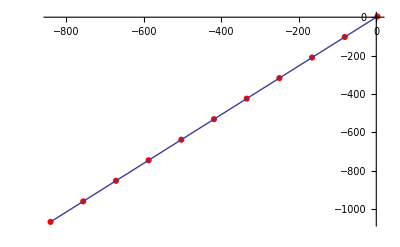

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  34

fixed point ~ -86.

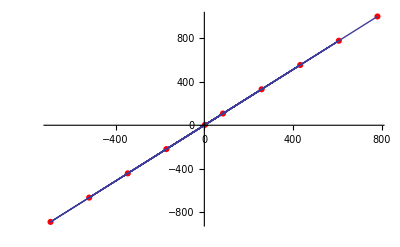

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  35

fixed point ~ -88.

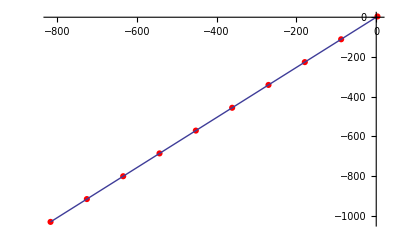

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  36

fixed point ~ -90.

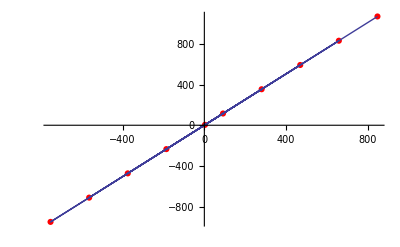

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  37

fixed point ~ -92.

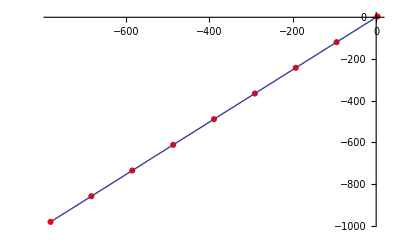

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  38

fixed point ~ -94.

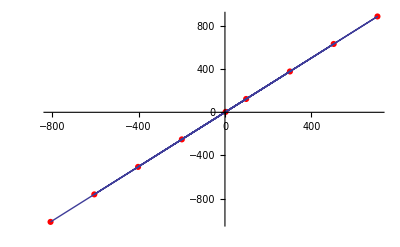

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  39

fixed point ~ -96.

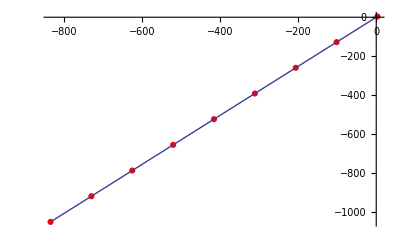

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  40

fixed point ~ -98.

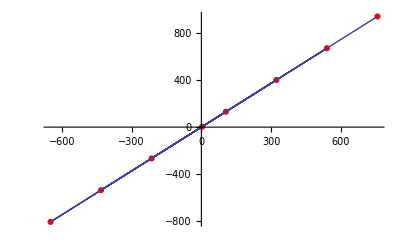

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  41

fixed point ~ -100.

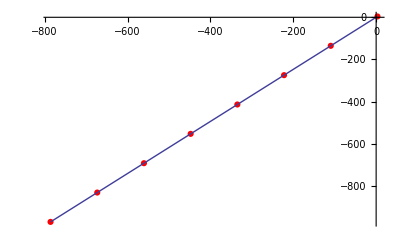

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  42

fixed point ~ -102.

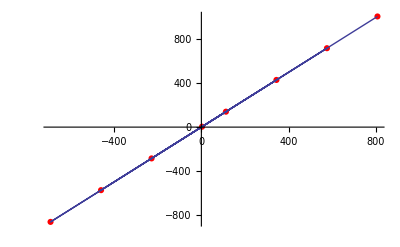

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  43

fixed point ~ -104.

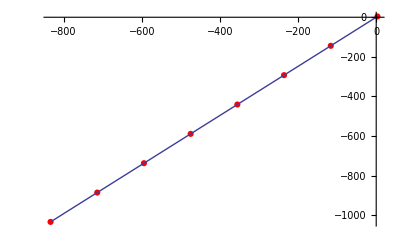

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  44

fixed point ~ -106.

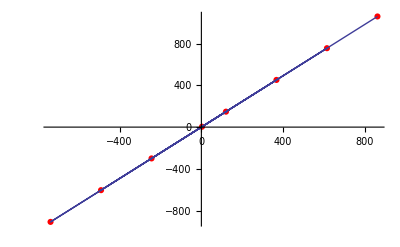

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  45

fixed point ~ -108.

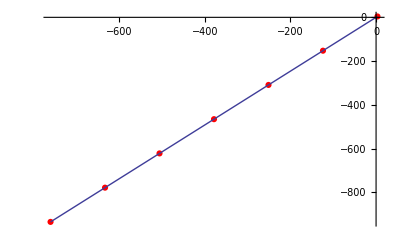

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  46

fixed point ~ -110.

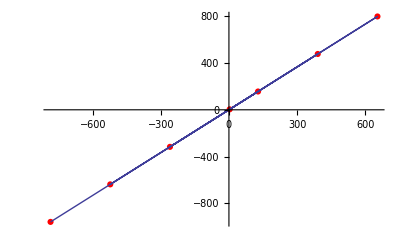

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  47

fixed point ~ -112.

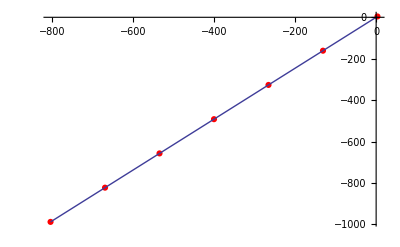

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  48

fixed point ~ -114.

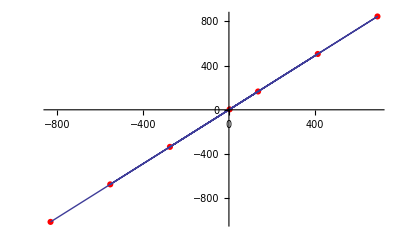

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  49

fixed point ~ -116.

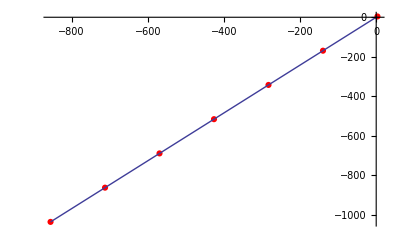

&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&

n  50

fixed point ~ -118.

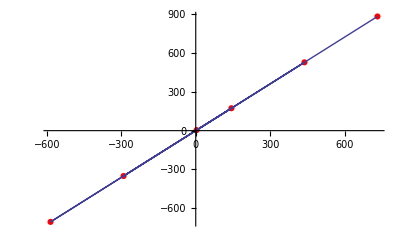

elasped seconds   1692.93075